```mathematica
A DCl molekula rezgési állapotai
```

```mathematica
(* DCl PES *)
D0=4.61/27.2116 (* hartree *);
α0=1.002 (* bohr^-1 *);
r0=2.4087 (* bohr *);
VX[r_]=D0*(Exp[-2*α0*(r-r0)]-2*Exp[-α0*(r-r0)]+1) (* hartree *);

(* DCl dipól, 1.8-3.8 bohr atommag-távolságokban *)

r0=2.4086 (* bohr *);
dX[r_]=0.4229+0.4629*((r-r0)/r0)^1-0.0452*((r-r0)/r0)^2−0.6306*((r-r0)/r0)^3−0.1219*((r-r0)/r0)^4 (* e*bohr *);

mD=2.01410178*1822.88848620 (* m_e *);
mCl35=34.96885269*1822.88848620 (* m_e *);
μDCl35=1/(1/mD+1/mCl35) (* m_e *);

Lpoti = 10 (* bohr *);
```

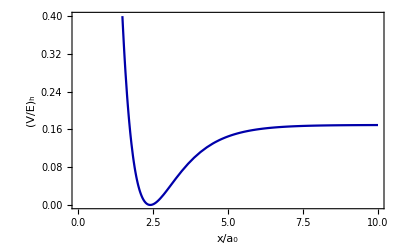

```mathematica
PotPlot= Plot[VX[r] ,{r,0,Lpoti},PlotRange->{{0,10},{0,0.4}},Frame->True, FrameLabel->{"x/a_0", Rotate[Text[Subscript[Style["V/E", Italic], "h"]],270 Degree]},  PlotStyle->Directive[Darker[Blue]], Axes->False]
Export[NotebookDirectory[]<>"pot_energia.eps",PotPlot];
```

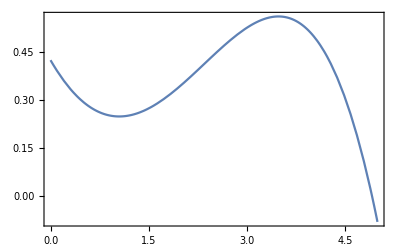

```mathematica
PotPlot= Plot[dX[r] ,{r,0,5},Frame->True,Axes->False]
```

### Fourier-DVR (gridpontok 0 és L között) primitív bázis: φ_k(x) = 1/(√L)ⅇ^(ⅈ(2π)/L k(x-L/2)), k = -n/2, ...,+n/2

```mathematica
n=100; (* bázisfüggvények száma *)
L=Lpoti; (* Fourier bázis periódushossza *)

(* Koordinátamátrix DVR-hez *)
Qmx=Table[0,{i,n},{j, n}];
Do[Qmx[[i,j]]=-(ⅈ*(-1)^(j+i)*L)/(2*π*(j-i)); Qmx[[j,i]]=-Qmx[[i,j]],{i,n},{j,i+1,n}];
Do[Qmx[[i,i]]=L/2,{i,n}];

q=Eigenvalues[N[Qmx]];
Tmx=Eigenvectors[N[Qmx]];
q=Sort[q];
```

```mathematica
(* Kinetikus energia mátrixa *)
Kmx=Table[0,{i,n},{j,n}];
Do[Kmx[[i,i]]=2*(π^2(i-1-n/2)^2)/(μDCl35*L^2),{i,n}];

(* Hamilton-mátrix *)
HDVR=Tmx.Kmx.Transpose[Conjugate[Tmx]];
Do[HDVR[[i,i]]=HDVR[[i,i]]+VX[q[[i]]],{i,n}]; 

Print["Legkisebb energia sajátértékek: " MatrixForm[Sort[Chop[Take[219474.63*Eigenvalues[N[HDVR], -5]]]]]]
```

Legkisebb energia sajátértékek:  (1078.37
3187.49
5233.14
7215.32
9134.02)

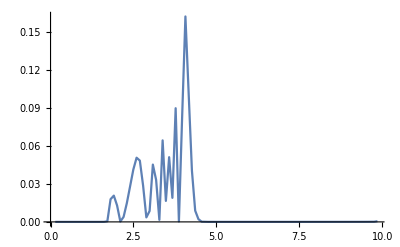

```mathematica
eigvec = Eigenvectors[N[HDVR]];
gridlist=Table[{q[[k]],Abs[eigvec[[n-15,k]]]^2},{k,n}];
ListLinePlot[gridlist, PlotRange->All]
```

```mathematica
Clear[hw]
Clear[g]

Wmx=Table[0,{i,n},{j,n}];
Do[Wmx[[i,i]]=dX[q[[i]]],{i,n}];

Hm=KroneckerProduct[HDVR,({{1, 0}, {0, 1}})];
Hr=KroneckerProduct[IdentityMatrix[n],({{0, 0}, {0, hw}})];
W=-g*KroneckerProduct[Wmx,({{0, 1}, {1, 0}})];
```

```mathematica
A=Hm+Hr+W;
hw = 0/219474.63;
g=1500/219474.63;
```

```mathematica
Print["Legkisebb összenergia sajátértékek: " MatrixForm[Sort[Chop[Take[219474.63*Eigenvalues[N[A]],-5]]]]]
```

Legkisebb összenergia sajátértékek:  (-2937.48
437.312
1035.04
1718.28
2534.27
3839.54
4175.32
4567.95
5897.15
6538.45)

## A p legkisebb rezgési sajátértékhez tartozó sajátállapot segítségével alkossunk egy új bázist. Ezen bázison HDVRp, valamint Wmxp mátrixelemeit.

```mathematica
p=5;
HDVRp=Table[0,{i,p},{j,p}];
Do[HDVRp[[i,i]]=Eigenvalues[N[HDVR]][[n-i+1]],{i,p}];
```

```mathematica
HDVRp // MatrixForm
```

(0.0049134-7.77329×10^-18 ⅈ | 0 | 0 | 0 | 0
0 | 0.0145233-1.13705×10^-17 ⅈ | 0 | 0 | 0
0 | 0 | 0.023844-2.26717×10^-17 ⅈ | 0 | 0
0 | 0 | 0 | 0.0328754+1.71859×10^-19 ⅈ | 0
0 | 0 | 0 | 0 | 0.0416177-4.90835×10^-18 ⅈ)

```mathematica
Wmxp=Table[0,{i,p},{j,p}];
```

```mathematica
Do[Wmxp[[i,j]]=Conjugate[eigvec[[n-i+1]]].(Wmx.eigvec[[n-j+1]]),{i,p},{j,p}];
```

```mathematica
Wmxp // MatrixForm
```

(0.426989-3.46945×10^-18 ⅈ | -0.0224289+0.00511768 ⅈ | 0.00208637-0.000994635 ⅈ | 0.000131296-0.0000812003 ⅈ | -6.71433×10^-7+5.23391×10^-7 ⅈ
-0.0224289-0.00511768 ⅈ | 0.435091-6.93889×10^-18 ⅈ | 0.0314139-0.0070421 ⅈ | 0.00398068-0.00136145 ⅈ | 0.000317394-0.000148578 ⅈ
0.00208637+0.000994635 ⅈ | 0.0314139+0.0070421 ⅈ | 0.443066+0. ⅈ | -0.0386412+0.00422938 ⅈ | -0.00609851+0.00134642 ⅈ
0.000131296+0.0000812003 ⅈ | 0.00398068+0.00136145 ⅈ | -0.0386412-0.00422938 ⅈ | 0.450851+0. ⅈ | -0.0438018+0.00476119 ⅈ
-6.71433×10^-7-5.23391×10^-7 ⅈ | 0.000317394+0.000148578 ⅈ | -0.00609851-0.00134642 ⅈ | -0.0438018-0.00476119 ⅈ | 0.458367+0. ⅈ)

```mathematica
WmxpDebye=Wmxp*5.291772109*10^(-11)*1.602176634*10^(-19)/(3.335640952*10^(-30));
```

```mathematica
WmxpDebye // MatrixForm
```

(1.0853-8.81845×10^-18 ⅈ | -0.0570085+0.0130078 ⅈ | 0.00530303-0.00252811 ⅈ | 0.000333721-0.00020639 ⅈ | -1.70661×10^-6+1.33033×10^-6 ⅈ
-0.0570085-0.0130078 ⅈ | 1.10589-1.76369×10^-17 ⅈ | 0.0798462-0.0178992 ⅈ | 0.0101179-0.00346047 ⅈ | 0.000806736-0.000377647 ⅈ
0.00530303+0.00252811 ⅈ | 0.0798462+0.0178992 ⅈ | 1.12616+0. ⅈ | -0.0982161+0.01075 ⅈ | -0.0155009+0.00342225 ⅈ
0.000333721+0.00020639 ⅈ | 0.0101179+0.00346047 ⅈ | -0.0982161-0.01075 ⅈ | 1.14595+0. ⅈ | -0.111333+0.0121017 ⅈ
-1.70661×10^-6-1.33033×10^-6 ⅈ | 0.000806736+0.000377647 ⅈ | -0.0155009-0.00342225 ⅈ | -0.111333-0.0121017 ⅈ | 1.16505+0. ⅈ)

```mathematica
Clear[hw]
Clear[g]
```

```mathematica
Hm=KroneckerProduct[HDVRp,({{1, 0}, {0, 1}})];
Hr=KroneckerProduct[IdentityMatrix[p],({{0, 0}, {0, hw}})];
W=-g*KroneckerProduct[Wmxp,({{0, 1}, {1, 0}})];
```

```mathematica
A=Hm+Hr+W;
lowerlimit = 0/219474.63;
upperlimit = 5000/219474.63;
energies=219474.63*Eigenvalues[A];
```

```mathematica
EigPlot3D= Plot3D[{Re[energies[[2]]],Re[energies[[3]]]},{hw,lowerlimit, upperlimit},{g,lowerlimit, upperlimit},AxesLabel->{"ℏω/E_h","  g/(a_0e/E_h)","E_i/cm^-1  "}, PlotStyle->{ColorData [97,2],ColorData [97,3]} ]
Export[NotebookDirectory[]<>"eig_plot_3D.eps",EigPlot3D];
```

-Graphics3D-

```mathematica
g=1500/219474.63;
data1=Table[Re[energies[[1]]],{hw,lowerlimit, upperlimit, upperlimit/100}];
data2=Table[Re[energies[[2]]],{hw,lowerlimit, upperlimit, upperlimit/100}];
data3=Table[Re[energies[[3]]],{hw,lowerlimit, upperlimit, upperlimit/100}];
data4=Table[Re[energies[[4]]],{hw,lowerlimit, upperlimit, upperlimit/100}];
data5=Table[Re[energies[[5]]],{hw,lowerlimit, upperlimit, upperlimit/100}];
data6=Table[energies[[6]],{hw,lowerlimit, upperlimit, upperlimit/100}];
data7=Table[energies[[7]],{hw,lowerlimit, upperlimit, upperlimit/100}];
data8=Table[energies[[8]],{hw,lowerlimit, upperlimit, upperlimit/100}];
data9=Table[energies[[9]],{hw,lowerlimit, upperlimit, upperlimit/100}];
data10=Table[energies[[10]],{hw,lowerlimit, upperlimit, upperlimit/100}];
```

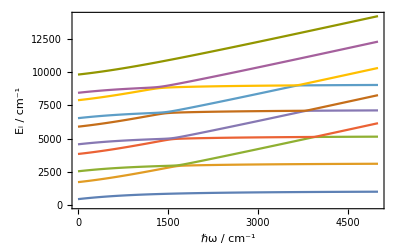

```mathematica
EigPlot= ListLinePlot[{data1, data2, data3, data4, data5, data6, data7, data8, data9, data10},DataRange->{0,5000}, Frame->True, FrameLabel->{"ℏω / cm^-1", "E_i / cm^-1"}]
Export[NotebookDirectory[]<>"eig_plot.eps",EigPlot];
```

```mathematica
data2=Table[Re[energies[[2]]],{hw, 1500/219474.63,2000/219474.63, upperlimit/1000}];
data3=Table[Re[energies[[3]]],{hw,1500/219474.63, 2000/219474.63, upperlimit/1000}];
```

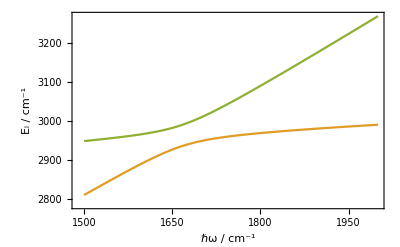

```mathematica
EigPlotzoom= ListLinePlot[{data2, data3},DataRange->{1500,2000}, Frame->True, PlotStyle->{ColorData [97,2],ColorData [97,3]}, FrameLabel->{"ℏω / cm^-1", "E_i / cm^-1"}]
Export[NotebookDirectory[]<>"eig_plot_zoom.eps",EigPlotzoom];
```

## Statisztikus termodinamika

```mathematica
Clear[g];
k=1.38064852*10^(-23);
NA=6.0221406*10^23;
R=8.314462618153;
h=6.62607004*10^(-34);
M=(mD+mCl35)/1822.88848620;
beta=1/(k*T);
hw = 1500/219474.63;


Hm=KroneckerProduct[HDVRp,({{1, 0}, {0, 1}})];
Hr=KroneckerProduct[IdentityMatrix[p],({{0, 0}, {0, hw}})];

energiesinJouleM=Table[0,{i,2*p+1},{j,2*p}];

For[i=0,i<=2*p,i++,
g=i*500/219474.63;
W=-g*KroneckerProduct[Wmxp,({{0, 1}, {1, 0}})];
A=Hm+Hr+W;
energiesinJouleM[[i+1]]=Sort[Re[Eigenvalues[A]]]*4.359744722*10^(-18);
]
```

```mathematica
energiesinJouleM//MatrixForm
```

(2.14212×10^-20 | 5.12178×10^-20 | 6.33178×10^-20 | 9.31145×10^-20 | 1.03954×10^-19 | 1.3375×10^-19 | 1.43328×10^-19 | 1.73125×10^-19 | 1.81442×10^-19 | 2.11239×10^-19
2.08285×10^-20 | 5.18052×10^-20 | 6.27067×10^-20 | 9.37193×10^-20 | 1.03325×10^-19 | 1.34371×10^-19 | 1.42684×10^-19 | 1.7376×10^-19 | 1.80788×10^-19 | 2.11922×10^-19
1.91726×10^-20 | 5.3441×10^-20 | 6.10077×10^-20 | 9.53911×10^-20 | 1.0159×10^-19 | 1.36066×10^-19 | 1.40927×10^-19 | 1.75452×10^-19 | 1.79049×10^-19 | 2.13814×10^-19
1.67197×10^-20 | 5.58047×10^-20 | 5.85567×10^-20 | 9.75803×10^-20 | 9.93139×10^-20 | 1.37541×10^-19 | 1.39366×10^-19 | 1.75777×10^-19 | 1.78666×10^-19 | 2.16585×10^-19
1.37267×10^-20 | 5.52765×10^-20 | 5.89845×10^-20 | 9.56397×10^-20 | 1.01155×10^-19 | 1.34766×10^-19 | 1.42043×10^-19 | 1.72723×10^-19 | 1.81665×10^-19 | 2.19932×10^-19
1.03785×10^-20 | 5.18984×10^-20 | 6.22545×10^-20 | 9.21784×10^-20 | 1.04508×10^-19 | 1.31216×10^-19 | 1.45487×10^-19 | 1.69138×10^-19 | 1.85202×10^-19 | 2.23649×10^-19
6.79451×10^-21 | 4.82408×10^-20 | 6.57984×10^-20 | 8.84408×10^-20 | 1.08132×10^-19 | 1.27398×10^-19 | 1.49193×10^-19 | 1.65308×10^-19 | 1.88996×10^-19 | 2.27609×10^-19
3.04991×10^-21 | 4.44157×10^-20 | 6.95047×10^-20 | 8.45347×10^-20 | 1.11919×10^-19 | 1.23413×10^-19 | 1.53056×10^-19 | 1.61331×10^-19 | 1.92953×10^-19 | 2.31734×10^-19
-8.07669×10^-22 | 4.04757×10^-20 | 7.332×10^-20 | 8.05147×10^-20 | 1.15803×10^-19 | 1.19326×10^-19 | 1.56745×10^-19 | 1.57538×10^-19 | 1.9702×10^-19 | 2.35976×10^-19
-4.74722×10^-21 | 3.64532×10^-20 | 7.63734×10^-20 | 7.72519×10^-20 | 1.15102×10^-19 | 1.19819×10^-19 | 1.53054×10^-19 | 1.61134×10^-19 | 2.01165×10^-19 | 2.40304×10^-19
-8.74801×10^-21 | 3.23693×10^-20 | 7.22373×10^-20 | 8.11743×10^-20 | 1.10867×10^-19 | 1.23843×10^-19 | 1.48863×10^-19 | 1.65241×10^-19 | 2.05366×10^-19 | 2.44697×10^-19)

#### Paraméteres energiaszintek esetén meghatározzuk a különféle termodinamikai mennyiségeket

```mathematica
Qvec=Table[Subscript[vec,i],{i,2*p+1}];
cpvec=Table[Subscript[vec,i],{i,2*p+1}];
cvvec=Table[Subscript[vec,i],{i,2*p+1}];
svec=Table[Subscript[vec,i],{i,2*p+1}];
uvec=Table[Subscript[vec,i],{i,2*p+1}];
hvec=Table[Subscript[vec,i],{i,2*p+1}];
fvec=Table[Subscript[vec,i],{i,2*p+1}];
gvec=Table[Subscript[vec,i],{i,2*p+1}];


For[i=0,i<=2*p,i++,
Qvec[[i+1]]=Chop[Sum[Exp[-beta*(energiesinJouleM[[i+1,j]]-energiesinJouleM[[i+1,1]])],{j,Length[energies]}]];
Q=Qvec[[i+1]];
U=k*T^2*D[Log[Q],T];
uvec[[i+1]]=U*NA;
F=-k*T*Log[Q];
fvec[[i+1]]=F*NA;
svec[[i+1]]=(uvec[[i+1]]-fvec[[i+1]])/T;
hvec[[i+1]]=uvec[[i+1]]+R*T;
gvec[[i+1]]=uvec[[i+1]]-T*svec[[i+1]]+R*T;
cvvec[[i+1]]=D[uvec[[i+1]],T];
cpvec[[i+1]]=cvvec[[i+1]]+R;
]

(* Ez a kódrészlet az alábbi cikk formuláit használja:
'Direct Evaluation of the Partition Function and Thermodynamic Data for Water at High Temperatures'

Q1momvec=Table[Subscript[vec,i],{i,2*p+1}];
Q2momvec=Table[Subscript[vec,i],{i,2*p+1}];

cptr=5/2*R;
geftr=R*(3/2*Log[M]+5/2*Log[T]+Log[(k/pres)*(2*Pi*k/(h^2))^(3/2)]);
Str=geftr+5/2*R;
v=R*T/pres;

For[i=0,i<=2*p,i++,
Qvec[[i+1]]=Chop[Sum[Exp[-beta*(energiesinJouleM[[i+1,j]]-energiesinJouleM[[i+1,1]])],{j,Length[energyvec]}]];
Q=Qvec[[i+1]];
Q1momvec[[i+1]]=T*D[Q,T];
Q2momvec[[i+1]]=T^2*D[D[Q,T],T]+2*Q1momvec[[i+1]];
cpvec[[i+1]]=R*(Q2momvec[[i+1]]/Q-(Q1momvec[[i+1]]/Q)^2)+cptr;
S=R*Q1momvec[[i+1]]/Q+R*Log[Q]+Str;
svec[[i+1]]=S*NA;
U=k*T*Q1momvec[[i+1]]/Q;
uvec[[i+1]]=U*NA;
cvvec[[i+1]]=D[u,T];
hvec[[i+1]]=uvec[[i+1]]+pres*v;
fvec[[i+1]]=uvec[[i+1]]-T*svec[[i+1]];
gvec[[i+1]]=uvec[[i+1]]-T*svec[[i+1]]+pres*v;
]

*)
```

```mathematica
upperlimit=1000;
```

```mathematica
myvec=Qvec;
```

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

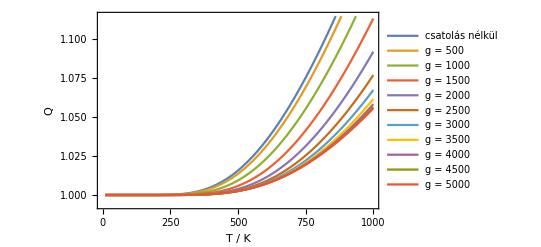

```mathematica
data1=Table[myvec[[1]],{T,10, upperlimit, upperlimit/100}];
data2=Table[myvec[[2]],{T,10, upperlimit, upperlimit/100}];
data3=Table[myvec[[3]],{T,10, upperlimit, upperlimit/100}];
data4=Table[myvec[[4]],{T,10, upperlimit, upperlimit/100}];
data5=Table[myvec[[5]],{T,10, upperlimit, upperlimit/100}];
data6=Table[myvec[[6]],{T,10, upperlimit, upperlimit/100}];
data7=Table[myvec[[7]],{T,10, upperlimit, upperlimit/100}];
data8=Table[myvec[[8]],{T,10, upperlimit, upperlimit/100}];
data9=Table[myvec[[9]],{T,10, upperlimit, upperlimit/100}];
data10=Table[myvec[[10]],{T,10, upperlimit, upperlimit/100}];data11=Table[myvec[[11]],{T,10, upperlimit, upperlimit/100}];
Qvecplot=ListLinePlot[{data1,data2,data3, data4,data5,data6,data7, data8,data9,data10,data11}, PlotLegends->Placed[LineLegend[{"csatolás nélkül","g = 500","g = 1000","g = 1500","g = 2000","g = 2500","g = 3000","g = 3500","g = 4000","g = 4500", "g = 5000"}, LegendLayout->{"Column",1}],Automatic],DataRange->{10,1000}, Frame->True, FrameLabel->{"T / K","Q"}]
Export[NotebookDirectory[]<>"Qvec.eps",Qvecplot];
```

### Delta mennyiségek

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1374.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1159.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1098.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

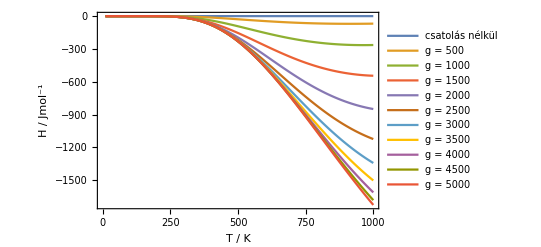

```mathematica
myvec=hvec;
data1=Table[myvec[[1]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];
data2=Table[myvec[[2]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];
data3=Table[myvec[[3]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];
data4=Table[myvec[[4]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];
data5=Table[myvec[[5]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];
data6=Table[myvec[[6]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];
data7=Table[myvec[[7]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];
data8=Table[myvec[[8]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];
data9=Table[myvec[[9]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];
data10=Table[myvec[[10]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];data11=Table[myvec[[11]]-myvec[[1]],{T,10, upperlimit, upperlimit/100}];
hdeltavecaplot=ListLinePlot[{data1,data2,data3, data4,data5,data6,data7, data8,data9,data10,data11}, PlotLegends->Placed[LineLegend[{"csatolás nélkül","g = 500","g = 1000","g = 1500","g = 2000","g = 2500","g = 3000","g = 3500","g = 4000","g = 4500", "g = 5000"}, LegendLayout->{"Column",1}],Automatic],DataRange->{10,1000}, Frame->True, FrameLabel->{"T / K","H / Jmol^-1"}]
Export[NotebookDirectory[]<>"hdeltavec.eps",hdeltavecaplot];
```

### 2 db fotonmódus

```mathematica
Clear[hw]
Clear[g]

Hm2=KroneckerProduct[HDVR, ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})];
Hr2=KroneckerProduct[IdentityMatrix[n],({{0, 0, 0}, {0, hw, 0}, {0, 0, 2*hw}})];
W2=g*KroneckerProduct[Wmx,({{0, 1, 0}, {1, 0, Sqrt[2]}, {0, Sqrt[2], 0}})];
```

```mathematica
A2=Hm2+Hr2-W2;
hw = 3000/219474.63;
g=0/219474.63;
```

```mathematica
Print["Legkisebb összenergia sajátértékek: " MatrixForm[Sort[Chop[Take[219474.63*Eigenvalues[N[A2],-6]]]]]]
```

Legkisebb összenergia sajátértékek:  (1499.2
4405.05
4499.2
7187.5
7405.05
7499.2)

```mathematica
Clear[hw]
Clear[g]
Hm2=KroneckerProduct[HDVR, ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})];
Hr2=KroneckerProduct[IdentityMatrix[n],({{0, 0, 0}, {0, hw, 0}, {0, 0, 2*hw}})];
W2=g*KroneckerProduct[Wmx,({{0, 1, 0}, {1, 0, Sqrt[2]}, {0, Sqrt[2], 0}})];
```

```mathematica
A2=Hm2+Hr2-W2;
upperlimit = 5000/219474.63;
energies2=219474.63*Eigenvalues[A2];
```

General::munfl: (1.79276×10^-15+5.06288×10^-15 ⅈ) (2.31417×10^-294-3.671×10^-294 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-3.31213×10^-15+2.06516×10^-15 ⅈ) (2.31417×10^-294-3.671×10^-294 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.72318×10^-15-5.83492×10^-16 ⅈ) (2.31417×10^-294-3.671×10^-294 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.